Lambda doublet splitting for BeO+.  MCH, April 19, 2020
Molecular constants from Journal of Physics B, Volume 41, Number 20, page 1 (2008).

```mathematica
B=0.37
```

0.37

```mathematica
A=-135
```

-135

```mathematica
Y=A/B
```

-364.865

```mathematica
p=-(4*A*B)(0.212/685.2+0.368/(685.2-1406.1)+0.273/(685.2-2053.3)+0.133/(685.2-2738.8))
```

-0.092984

```mathematica
q=-4*B*B(0.212/685.2+0.368/(685.2-1406.1)+0.273/(685.2-2053.3)+0.133/(685.2-2738.8))
```

0.000254845

```mathematica
X[J_]:=Abs[Sqrt[Y*(Y-4)+(J+1/2)^2]]
```

```mathematica
DV[J_]:=((p/2+q)*(-1+2/X[J]-Y/X[J])+(2*q)/X[J]*(J-0.5)*(J+1.5))*(J+0.5)
```

```mathematica
Z=Table[{J,DV[J]*3*10^4},{J,1.5,9.5,1}];
```

```mathematica
MatrixForm[Z]
```

(1.5 | 0.250076
2.5 | 1.07758
3.5 | 2.74799
4.5 | 5.54215
5.5 | 9.74085
6.5 | 15.6248
7.5 | 23.4744
8.5 | 33.5702
9.5 | 46.1922)

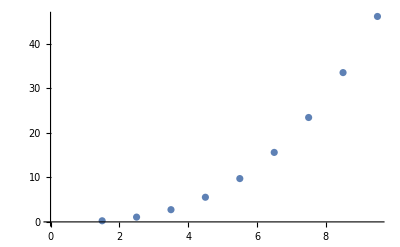

```mathematica
ListPlot[Z]
```